```mathematica
SetDirectory@NotebookDirectory[];
Import["QuESTlink.m"];
CreateLocalQuESTEnv["quest_link"];
```

## Parameters

```mathematica
model=4;(*4:S-Q error;*)
numQb=6;
numGt=numQb^2;
seed=-1;
ϵ=0.002;
SamSize=10000;
```

```mathematica
CreateFile["CS-m"<>ToString[model]<>"-Q"<>ToString[numQb]<>"-G"<>ToString[numGt]<>"-e"<>ToString[ϵ]<>".dat"];
file=File["CS-m"<>ToString[model]<>"-Q"<>ToString[numQb]<>"-G"<>ToString[numGt]<>"-e"<>ToString[ϵ]<>".dat"];
Data={};
AppendTo[Data,"model:"<>ToString[model]];
AppendTo[Data,"numQb:"<>ToString[numQb]];
AppendTo[Data,"numGt:"<>ToString[numGt]];
AppendTo[Data,"seed:"<>ToString[seed]];
AppendTo[Data,"eps:"<>ToString[ϵ]];
AppendTo[Data,"SamSize:"<>ToString[SamSize]];
AppendTo[Data,""];
Export[file,Data];
```

## QC

```mathematica
ψIN=CreateQureg[numQb];
ψOUT=CreateQureg[numQb];
ψWP=CreateQureg[numQb];
ρIN=CreateDensityQureg[numQb];
ρOUT=CreateDensityQureg[numQb];
ρWP=CreateDensityQureg[numQb];
```

## Gates

```mathematica
Clifford = Table[i*N[π,12]/2,{i,0,3,1}];
```

```mathematica
θ=RandomReal[{0,2*N[π,12]},3*numQb+6*numGt];
```

## Circuits

```mathematica
GateGraphGen[numQb_,numGt_,seed_]:=(
GateGraph={};
If[seed==-1,
depth=Ceiling[numGt/Floor[numQb/2]];
qINI=0;
Do[(
Do[(
AppendTo[GateGraph,q];
AppendTo[GateGraph,Mod[q+1,numQb]];
),{q,qINI,numQb-1,2}];
qINI=1-qINI;
),{t,0,depth-1,1}];
AppendTo[GateGraph,Table[0,numQb-1]]
];
If[seed!=-1,
SeedRandom[seed];
Do[(
q=RandomInteger[{0,numQb-1}];
dis=RandomInteger[{1,numQb-1}];
AppendTo[GateGraph,q];
AppendTo[GateGraph,Mod[q+dis,numQb]];
),{t,0,numGt-1,1}];
AppendTo[GateGraph,RandomInteger[{0,1},numQb-1]]
];
Return[GateGraph]
)
GateGraph=GateGraphGen[numQb,numGt,seed]
```

{0,1,2,3,4,5,1,2,3,4,5,0,0,1,2,3,4,5,1,2,3,4,5,0,0,1,2,3,4,5,1,2,3,4,5,0,0,1,2,3,4,5,1,2,3,4,5,0,0,1,2,3,4,5,1,2,3,4,5,0,0,1,2,3,4,5,1,2,3,4,5,0,{0,0,0,0,0}}

```mathematica
circuitIdeal[numQb_,numGt_,GateGraph_,θ_]:=(
circ={};
Do[(
AppendTo[circ,Subscript[Rz, q][θ[[3*q+1]]]];
AppendTo[circ,Subscript[Rx, q][θ[[3*q+2]]]];
AppendTo[circ,Subscript[Rz, q][θ[[3*q+3]]]];
),{q,0,numQb-1,1}];
Do[(
q1=GateGraph[[2*t+1]];
q2=GateGraph[[2*t+2]];
AppendTo[circ,Subscript[C, q1][Subscript[Z, q2]]];
AppendTo[circ,Subscript[Rz, q1][θ[[3*numQb+6*t+1]]]];
AppendTo[circ,Subscript[Rx, q1][θ[[3*numQb+6*t+2]]]];
AppendTo[circ,Subscript[Rz, q1][θ[[3*numQb+6*t+3]]]];
AppendTo[circ,Subscript[Rz, q2][θ[[3*numQb+6*t+4]]]];
AppendTo[circ,Subscript[Rx, q2][θ[[3*numQb+6*t+5]]]];
AppendTo[circ,Subscript[Rz, q2][θ[[3*numQb+6*t+6]]]];
),{t,0,numGt-1,1}];
Do[(
If[GateGraph[[2*numGt+1,q]]==1,AppendTo[circ,Subscript[C, q][Subscript[X, 0]]]];
),{q,1,numQb-1,1}];
Return[circ]
)
```

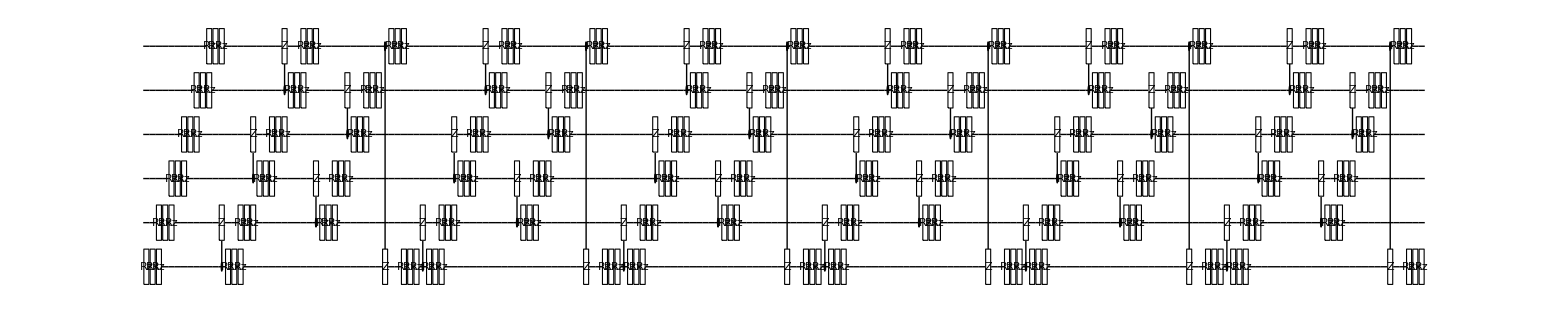

```mathematica
circI=circuitIdeal[numQb,numGt,GateGraph,θ];
DrawCircuit@circI
```

```mathematica
circuitNoisy[numQb_,numGt_,GateGraph_,θ_,model_,ϵ_]:=(
circ={};
Do[(
the1=θ[[3*q+1]];
the2=θ[[3*q+2]];
the3=θ[[3*q+3]];
AppendTo[circ,Subscript[Rz, q][the1]];
AppendTo[circ,Subscript[Rx, q][the2]];
AppendTo[circ,Subscript[Rz, q][the3]];
AppendTo[circ,Subscript[Depol, q][ϵ/10*(the1+the2+the3)/(2*N[π,12])]];
),{q,0,numQb-1,1}];
Do[(
q1=GateGraph[[2*t+1]];
q2=GateGraph[[2*t+2]];
AppendTo[circ,Subscript[C, q1][Subscript[Z, q2]]];AppendTo[circ,Subscript[Depol, q1,q2][ϵ]];
the1=θ[[3*numQb+6*t+1]];
the2=θ[[3*numQb+6*t+2]];
the3=θ[[3*numQb+6*t+3]];
AppendTo[circ,Subscript[Rz, q1][the1]];
AppendTo[circ,Subscript[Rx, q1][the2]];
AppendTo[circ,Subscript[Rz, q1][the3]];
AppendTo[circ,Subscript[Depol, q1][ϵ/10*(the1+the2+the3)/(2*N[π,12])]];
the1=θ[[3*numQb+6*t+4]];
the2=θ[[3*numQb+6*t+5]];
the3=θ[[3*numQb+6*t+6]];
AppendTo[circ,Subscript[Rz, q2][the1]];
AppendTo[circ,Subscript[Rx, q2][the2]];
AppendTo[circ,Subscript[Rz, q2][the3]];
AppendTo[circ,Subscript[Depol, q2][ϵ/10*(the1+the2+the3)/(2*N[π,12])]];
),{t,0,numGt-1,1}];
Do[(
If[GateGraph[[2*numGt+1,q]]==1,AppendTo[circ,Subscript[C, q][Subscript[X, 0]]]];
),{q,1,numQb-1,1}];
Return[circ]
)
```

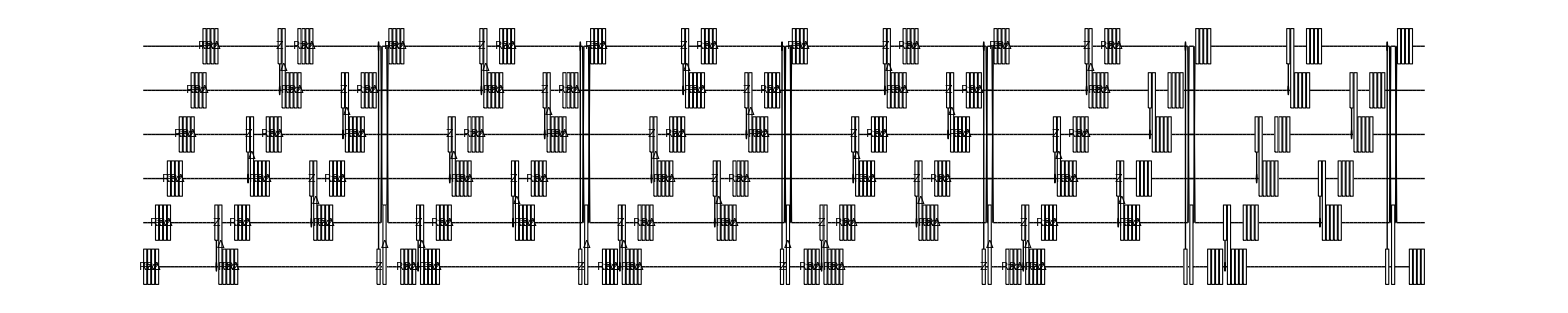

```mathematica
circN=circuitNoisy[numQb,numGt,GateGraph,θ,model,ϵ];
DrawCircuit@circN
```

## Sampling

```mathematica
SamplingU[numQb_,numGt_,GateGraph_,model_,ϵ_,SamSize_]:=(
Err={};
Fid={};
Do[(
θ=RandomReal[{0,2*N[π,12]},3*numQb+6*numGt];
circI=circuitIdeal[numQb,numGt,GateGraph,θ];
circN=circuitNoisy[numQb,numGt,GateGraph,θ,model,ϵ];
ApplyCircuit[circI,ψIN,ψOUT];
ZI=CalcExpecPauliSum[ψOUT,Subscript[Z, 0],ψWP];
ApplyCircuit[circN,ρIN,ρOUT];
ZN=CalcExpecPauliSum[ρOUT,Subscript[Z, 0],ρWP];
AppendTo[Err,ZN-ZI];
AppendTo[Fid,1-CalcFidelity[ρOUT,ψOUT]];
),SamSize];
Return[{Err,Fid}]
)
```

```mathematica
SamplingC[numQb_,numGt_,GateGraph_,model_,ϵ_,SamSize_]:=(
Err={};
Fid={};
Do[(
θ=RandomChoice[Clifford,3*numQb+6*numGt];
circI=circuitIdeal[numQb,numGt,GateGraph,θ];
circN=circuitNoisy[numQb,numGt,GateGraph,θ,model,ϵ];
ApplyCircuit[circI,ψIN,ψOUT];
ZI=CalcExpecPauliSum[ψOUT,Subscript[Z, 0],ψWP];
ApplyCircuit[circN,ρIN,ρOUT];
ZN=CalcExpecPauliSum[ρOUT,Subscript[Z, 0],ρWP];
AppendTo[Err,ZN-ZI];
AppendTo[Fid,1-CalcFidelity[ρOUT,ψOUT]];
),SamSize];
Return[{Err,Fid}]
)
```

## Simulation

Tue 18 Feb 2020 15:51:44GMT+8.

{0,1,2,3,4,5,1,2,3,4,5,0,0,1,2,3,4,5,1,2,3,4,5,0,0,1,2,3,4,5,1,2,3,4,5,0,0,1,2,3,4,5,1,2,3,4,5,0,0,1,2,3,4,5,1,2,3,4,5,0,0,1,2,3,4,5,1,2,3,4,5,0,{0,0,0,0,0}}

Tue 18 Feb 2020 15:51:45GMT+8.

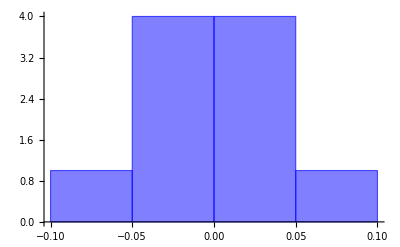

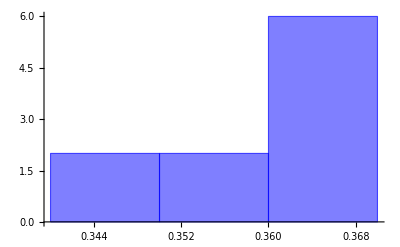

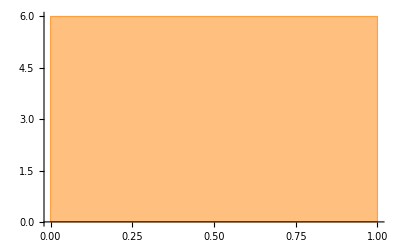

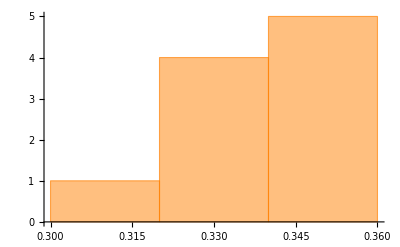

```mathematica
StartTime = Now
GateGraph=GateGraphGen[numQb,numGt,seed]
US=SamplingU[numQb,numGt,GateGraph,model,ϵ,SamSize];
CS=SamplingC[numQb,numGt,GateGraph,model,ϵ,SamSize];
EndTime = Now

Histogram[US[[1]],ChartStyle->Opacity[.5,Blue]]
Histogram[US[[2]],ChartStyle->Opacity[.5,Blue]]
Histogram[CS[[1]],ChartStyle->Opacity[.5,Orange]]
Histogram[CS[[2]],ChartStyle->Opacity[.5,Orange]]

AppendTo[Data,"US-Err:"];AppendTo[Data,US[[1]]];AppendTo[Data,""];
AppendTo[Data,"US-Fid:"];AppendTo[Data,US[[2]]];AppendTo[Data,""];
AppendTo[Data,"CS-Err:"];AppendTo[Data,CS[[1]]];AppendTo[Data,""];
AppendTo[Data,"CS-Fid:"];AppendTo[Data,CS[[2]]];AppendTo[Data,""];
AppendTo[Data,"Start Time: "<>ToString[StartTime]];
AppendTo[Data,"End Time: "<>ToString[EndTime]];
Export[file,Data];
```

```mathematica
MUS=Table[Moment[US[[1]],m],{m,1,10,1}]
MCS=Table[Moment[CS[[1]],m],{m,1,10,1}]
MUS=Table[Moment[US[[2]],m],{m,1,10,1}]
MCS=Table[Moment[CS[[2]],m],{m,1,10,1}]
```

{0.00424549,0.00138715,0.0000167745,6.2817×10^-6,1.19028×10^-7,3.37663×10^-8,8.74361×10^-10,1.88437×10^-10,6.13313×10^-12,1.067×10^-12}

{-4.28043×10^-17,8.65753×10^-33,-1.10924×10^-48,1.90548×10^-64,-3.04018×10^-80,5.25247×10^-96,-9.0636×10^-112,1.60784×10^-127,-2.87517×10^-143,5.20215×10^-159}

{0.358519,0.128583,0.0461333,0.0165577,0.00594487,0.00213519,0.000767151,0.000275724,0.0000991326,0.0000356536}

{0.336842,0.113608,0.038364,0.0129705,0.00439023,0.00148763,0.000504618,0.000171345,0.0000582375,0.0000198125}